```mathematica
SetDirectory[NotebookDirectory[]]
Import["GraphPartition.m"]
<< GraphPartition`
$Context
```

C:\Users\Chuqian\Desktop\research\graphPartitioning

Global`

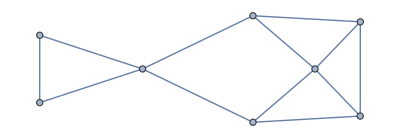
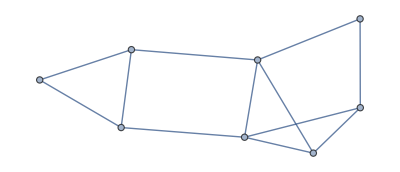
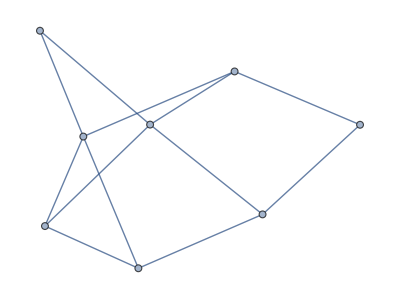

```mathematica
System`RandomGraph[DegreeGraphDistribution[{3,4,2,3,3,4,2,3}],3]
```

```mathematica
(*Neighbors[i_,j_, m_,n_,dist_] := Select[Complement[Flatten[Table[{i+di, i+dj},{di,-dist,dist},{dj,-dist,dist}],1],{{i,j}}],
1<=First[#]<=5 && 1≤Last[#]≤4 &]*)
```

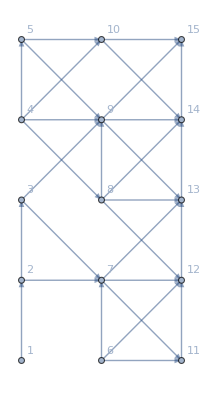

{1<->2,2<->3,2<->7,3<->9,3<->7,4<->10,4<->8,4<->9,5<->9,5<->4,5<->10,6<->11,6<->7,6<->12,7<->12,7<->13,8<->12,8<->14,9<->15,9<->13,9<->8,10<->15,11<->12,11<->7,13<->12,13<->14,13<->8,14<->10,14<->15,14<->9}

```mathematica
RandomGrid1[m_,n_,maxDist_:1, maxDegree_:4]:= Module[{elist={},
vlist = Range[1,m*n],
vcoords= Flatten[Table[{i,j},{i,1,m},{j,1,n}],1]},

Vertex1D[ij_] := (First[ij]-1)*n+Last[ij];
Neighbors[i_,j_,dist_] := Select[Flatten[Table[{i+di, j+dj},{di,-dist,dist},{dj,-dist,dist}],1],
1<=First[#]≤m && 1≤Last[#]≤n && #≠{i,j}&];
elist={};
Do[With[{newE = {Vertex1D[{i,j}],Vertex1D[adj]}},
AppendTo[elist,newE]],{i,1,m},{j,1,n},{adj, RandomChoice[Neighbors[i,j,maxDist],maxDegree]}]
elist =DeleteDuplicates[elist,#1==#2||#1==Reverse[#2]& ];
newG=System`Graph[vlist,elist,VertexCoordinates->vcoords,
System`VertexWeight->Table[1/Length[vlist], Length[vlist]],System`EdgeWeight-> Table[1,Length[elist]],
System`VertexLabels->Automatic,
System`EdgeStyle->Directive[Opacity[0.5], Thick], EdgeShapeFunction->"Arrow"];
newG (*UndirectedGraph[newG]*)]
(*m=4;
n=4;
maxDist = 1;
maxDegree = 2;
*)

g=RandomGrid1[3,5]
EdgeList[g]
```

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,3 3],0<VertexDistance[i,#1,3,3]≤1^2&],RandomInteger[{0,2}]]} does not have appropriate bounds.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,3 3],0<VertexDistance[i,#1,3,3]≤1^2&],RandomInteger[{0,2}]]} does not have appropriate bounds.

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice::lrwl will be suppressed during this calculation.

Table::iterb: Iterator {j,RandomChoice[Select[Range[i+1,3 3],0<VertexDistance[i,#1,3,3]≤1^2&],RandomInteger[{0,2}]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

EdgeAdd::inv: The argument Table[i<->j,{i,1,8},{j,RandomChoice[Select[Range[i+1,3 3],0<VertexDistance[i,Slot[«1»],3,3]≤1^2&],RandomInteger[{0,2}]]}] in EdgeAdd[Graph[<9>, <12>], Table[i <-> j, {i, 1, 8}, {j, RandomChoice[Select[Range[Plus[<<2>>], Times[<<2>>]], Inequality[<<5>>] & ], RandomInteger[{0, 2}]]}]] is not a valid edge.

General::stop: Further output of EdgeAdd::inv will be suppressed during this calculation.

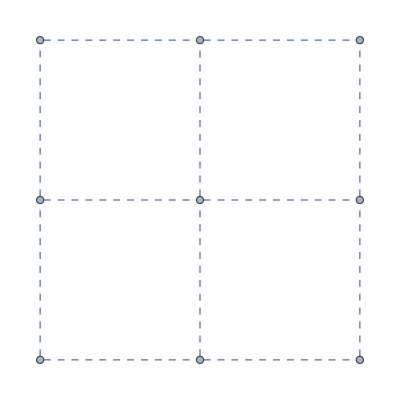
Graph[EdgeAdd[-Graphics-,Table[i<->j,{i,1,8},{j,RandomChoice[Select[Range[i+1,3 3],0<VertexDistance[i,#1,3,3]≤1^2&],RandomInteger[{0,2}]]}]],VertexWeight→{},EdgeWeight→Automatic]

```mathematica
RandomGrid2[m_,n_,maxDist_:1]:= Module[{newE},
g= System`GridGraph[{m,n},System`EdgeStyle->Directive[Dashed,Thick]
(*, EdgeShapeFunction->"Arrow"*)];
VertexDistance[i_,j_] :=
With[{x1=Mod[i-1,m], x2=Mod[j-1,m],y1=Quotient[i-1,m],y2=Quotient[j-1,m]},((x1-x2)^2+(y1-y2)^2)^(1/2)];
newE = Flatten[Table[UndirectedEdge[i,j],{i,1,m*n-1},
{j, RandomChoice[
Select[Range[i+1,m*n],0<VertexDistance[i,#,m,n]≤maxDist^2&]
,RandomInteger[{0,2}]]}],1];
g=Graph[System`EdgeAdd[g,newE],System`VertexWeight->Table[1/Length[m*n], Length[m*n]],System`EdgeWeight-> Automatic]]

g= RandomGrid2[3,3]
```

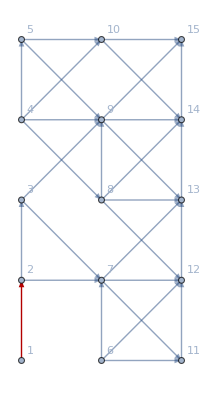

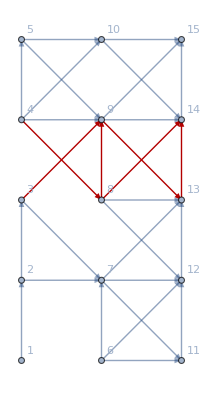

{6.06922×10^-16,0.470439,0.829655,2.04463,2.43313}

-Graphics-

```mathematica
(*GG = System`GridGraph[{3,4}, VertexLabels->Automatic,VertexWeight->Table[1/12,12]]*)
(*ShowSpectralCut[newG]*)
ShowSpectralCut[g]
ShowIsoperimetricCut[g]
ShowMultipleFiedlerCut[g]
```

```mathematica
Plot performances on GridGraphs
```

Range::range: Range specification in Range[1,n^2] does not have appropriate bounds.

Table::iterb: Iterator {i,1,n} does not have appropriate bounds.

Do::iterb: Iterator {i,1,n} does not have appropriate bounds.

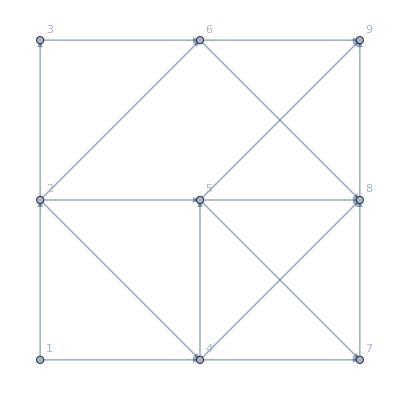

```mathematica
RandomGrid[n_] = RandomGrid1[n,n];

RandomGrid1[3,3]
```

```mathematica
SquareGrid[n_] := System`GridGraph[{n,n}, 
VertexLabels->If[n<10,Automatic,None],VertexWeight->Table[1/n/n,n*n], EdgeWeight->Automatic];
graphs = Map[RandomGrid1[#,#,  max]&, Range[3,18,3]];

SpectralMetrics = Map[EvaluatePartitionAlg[SpectralAlg, #]&, graphs];
SpectralTimes = Transpose[SpectralMetrics][[1]]
SpectralObjs = Transpose[SpectralMetrics][[2]]
IsoperimetricMetrics = Map[EvaluatePartitionAlg[IsoperimetricAlg, #]&, graphs];
IsoperimetricTimes = Transpose[IsoperimetricMetrics][[1]]
IsoperimetricObjs = Transpose[IsoperimetricMetrics][[2]]
MultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg, #]&, graphs];
MultipleFiedlerTimes = Transpose[MultipleFiedlerMetrics][[1]]
MultipleFiedlerObjs = Transpose[MultipleFiedlerMetrics][[2]]
```

Eigensystem::arh: Because finding 144 out of the 144 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 225 out of the 225 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 324 out of the 324 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

{0.,0.03125,0.171875,0.28125,0.546875,1.01563}

{45/2,144/5,5103/88,19440/299,455625/4897,33696/323}

{0.,0.015625,0.078125,0.234375,0.53125,0.96875}

{45/2,144/5,39366/649,23328/299,50625/472,368/3}

{1.77636×10^-15,1.61,2.19171,3.,3.90427}

{-6.5534×10^-17,0.271507,0.395013,0.735666,1.02019}

{-4.11194×10^-17,0.192566,0.208289,0.369166,0.727968}

{2.31296×10^-18,0.0998107,0.108068,0.195329,0.377432}

{2.51651×10^-17,0.0677633,0.0782836,0.140501,0.273707}

{6.16791×10^-18,0.0467401,0.0482243,0.0953544,0.187719}

{0.,0.03125,0.140625,0.671875,2.1875,2.03125}

{45/2,3888/155,6561/110,207360/2783,46575/464,7128/65}

```mathematica
EvaluatePartitionAlg[SpectralAlg, RandomGrid1[3,4]]
```

{0.015625,20,{2<->3,3<->6,7<->6,7<->10,10<->11}}

```mathematica
graphs = Map[SquareGrid[#]&, Range[10,50,5]];
EvaluatePartitionAlg[SpectralAlg, graphs[[3]]]
```

EvaluatePartitionAlg[SpectralAlg,SquareGrid[20]]

```mathematica
MultipleFiedlerObjs
```

{27/2,27,81/2,54,135/2,1994544/24563}

{Spectral,Isoperimetric,MultipleFiedler}

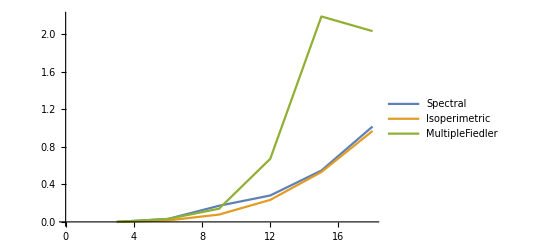

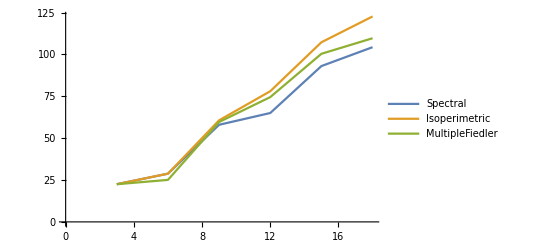

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes},PlotLegends->legends, DataRange->{3,18}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs}, PlotLegends->legends, DataRange->{3,18}]
```

```mathematica
NewMultipleFiedlerMetrics = Map[EvaluatePartitionAlg[MultipleFiedlerAlg , #]&, graphs];
NewMultipleFiedlerTimes = Transpose[NewMultipleFiedlerMetrics][[1]]
NewMultipleFiedlerObjs = Transpose[NewMultipleFiedlerMetrics][[2]]
```

{1.77636×10^-17,0.381964,0.38197,0.763929,1.38175}

{-9.28077×10^-17,0.152238,0.152244,0.304484,0.585771}

{-9.1754×10^-17,0.0810139,0.0810141,0.162028,0.31749}

{-6.11756×10^-17,0.0501441,0.0501442,0.100288,0.198062}

{-9.94975×10^-17,0.0340538,0.0340538,0.0681076,0.135056}

{-1.00475×10^-16,0.0246233,0.0246233,0.0492466,0.0978869}

{0.015625,0.109375,0.28125,0.671875,1.23438,2.3125}

{125/6,512/15,1331/28,2744/45,4913/66,8000/91}

{Spectral,Isoperimetric,MultipleFiedler,NewMultipleFiedler}

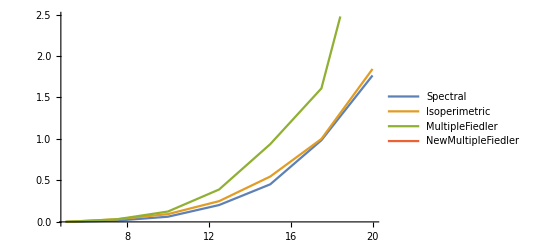

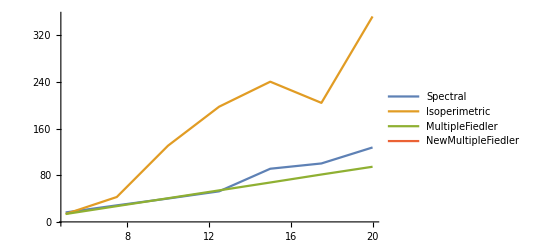

```mathematica
legends = {"Spectral","Isoperimetric","MultipleFiedler","NewMultipleFiedler"}
ListLinePlot[{SpectralTimes, IsoperimetricTimes, MultipleFiedlerTimes,NewMultipleFiedlerTimes},PlotLegends->legends, DataRange->{5,20}]
ListLinePlot[{SpectralObjs, IsoperimetricObjs, MultipleFiedlerObjs,NewMultipleFiedlerObjs}, PlotLegends->legends, DataRange->{5,20}]
```

```mathematica
{1,2,3,4,5}[[-1]]
```

5

```mathematica
SpannerGraph[n] := {}
```

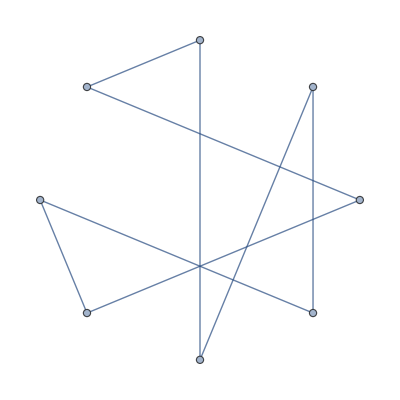
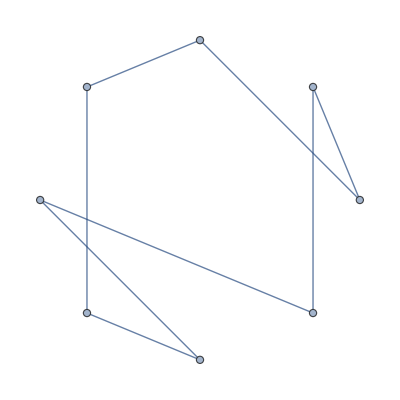
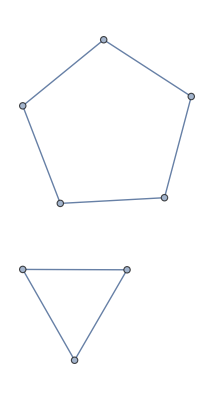

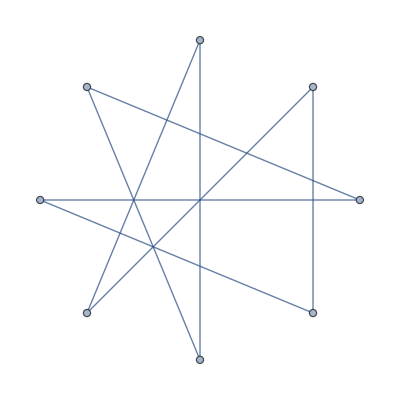

```mathematica
spanners=System`RandomGraph[DegreeGraphDistribution[{2,2,2,2,2,2,2,2}],3]
```

{4.44089×10^-15,0.405945,0.4502,1.2452,1.43602}

{7.10543×10^-15,0.428593,0.500921,1.26054,1.40478}

{2.66454×10^-15,0.280431,0.768772,1.22224,1.53495}

{6.21725×10^-15,0.331002,0.847204,1.13798,1.28996}

{5.32907×10^-15,0.396943,0.755748,1.04804,1.19909}

{4.44089×10^-15,0.361169,0.554836,0.84236,1.43142}

{4.44089×10^-15,0.395761,0.63339,1.04235,1.42939}

{3.55271×10^-15,0.435822,0.803404,0.972869,1.22498}

{3.55271×10^-15,0.39687,0.820591,1.05928,1.40591}

{-4.44089×10^-16,0.458377,0.763402,1.1507,1.37021}

{5.32907×10^-15,0.573571,0.669517,0.784734,1.25146}

{4.44089×10^-15,0.0950795,0.566175,1.04244,1.73606}

{3.55271×10^-15,0.443376,0.812682,1.10424,1.43436}

{5.82867×10^-16,0.408535,0.701434,1.13919,1.13919}

{4.44089×10^-15,0.286369,0.585786,0.764258,1.53252}

{4.44089×10^-15,0.47426,0.645666,0.735032,1.55644}

{4.44089×10^-15,0.40465,0.642494,0.934857,1.2382}

{4.44089×10^-15,0.411181,0.88657,0.936006,1.4839}

{-2.22045×10^-16,0.414206,0.751103,1.17235,1.27077}

{1.77636×10^-15,0.308364,0.750495,1.05928,1.42507}

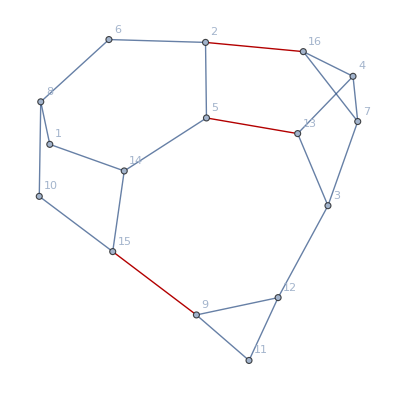
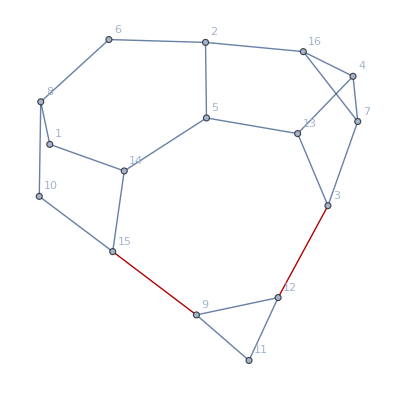
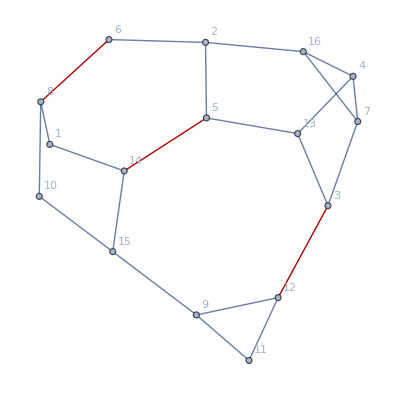
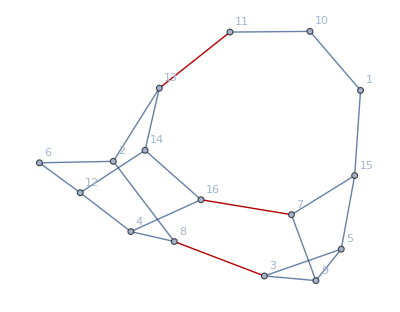
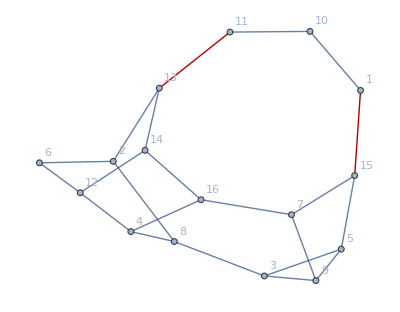
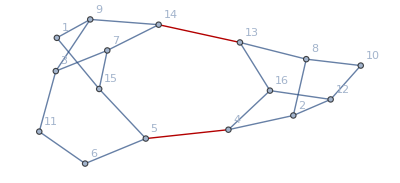
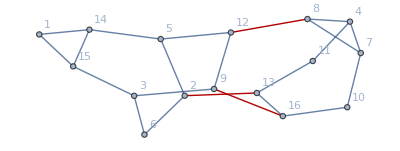
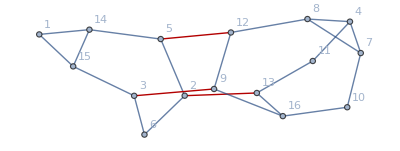
Spectral |  | Isoperimetric |  | MultipleFiedler |  | 
-Graphics- | 12. | -Graphics- | 13.1282 | -Graphics- | 12. | 
-Graphics- | 12. | -Graphics- | 13.1282 | -Graphics- | 13.1282 | 
-Graphics- | 8.12698 | -Graphics- | 8.12698 | -Graphics- | 8.12698 | 
-Graphics- | 12.1905 | -Graphics- | 12.1905 | -Graphics- | 12.1905 | 
-Graphics- | 12.8 | -Graphics- | 12.8 | -Graphics- | 12. | *
-Graphics- | 10.6667 | -Graphics- | 10.6667 | -Graphics- | 10.6667 | 
-Graphics- | 13.1282 | -Graphics- | 13.1282 | -Graphics- | 13.1282 | 
-Graphics- | 12. | -Graphics- | 12.1905 | -Graphics- | 12.1905 | 
-Graphics- | 12. | -Graphics- | 12. | -Graphics- | 12. | 
-Graphics- | 12.1905 | -Graphics- | 12.1905 | -Graphics- | 16. | 
-Graphics- | 16. | -Graphics- | 17.0667 | -Graphics- | 16. | 
-Graphics- | 4.26667 | -Graphics- | 4.26667 | -Graphics- | 4.65455 | 
-Graphics- | 13.1282 | -Graphics- | 13.1282 | -Graphics- | 13.1282 | 
-Graphics- | 12.1905 | -Graphics- | 12.8 | -Graphics- | 12.1905 | 
-Graphics- | 8. | -Graphics- | 8. | -Graphics- | 8. | 
-Graphics- | 12.8 | -Graphics- | 12.8 | -Graphics- | 16. | 
-Graphics- | 13.1282 | -Graphics- | 13.1282 | -Graphics- | 13.1282 | 
-Graphics- | 12. | -Graphics- | 12. | -Graphics- | 16. | 
-Graphics- | 13.1282 | -Graphics- | 13.1282 | -Graphics- | 13.1282 | 
-Graphics- | 9.30909 | -Graphics- | 9.30909 | -Graphics- | 9.30909 |

```mathematica
n=16;
spanners=System`RandomGraph[DegreeGraphDistribution[Table[RandomInteger[{2,3}],n]],20];
spanners =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/n,n], EdgeWeight->Automatic]&/@spanners;

examples=Map[With[{m1=EvaluatePartitionAlg[SpectralAlg, #], m2=EvaluatePartitionAlg[IsoperimetricAlg, #],
m3=EvaluatePartitionAlg[MultipleFiedlerAlg, #]},
{ShowCuttedEdges[#,m1[[3]]],N[m1[[2]]],
ShowCuttedEdges[#,m2[[3]]],N[m2[[2]]],
ShowCuttedEdges[#,m3[[3]]],N[m3[[2]]],
If [m1[[2]]>m3[[2]], "*",Nothing]}]&,spanners];
(*If [m1[[2]]<=m3[[2]], 
	{(*#,*)(*"Spectral",*)ShowCuttedEdges[#,m1[[3]]],N[m1[[2]]],
		(*"Isoperimetric",*)ShowCuttedEdges[#,m2[[3]]],N[m2[[2]]],
		(*"MultipleFiedler",*)ShowCuttedEdges[#,m3[[3]]],N[m3[[2]]]},
	Nothing]]&,spanners];*)

rowColors = Table[If[examples[[i, -1]]=="*",LightGreen,White] ,{i,1,Length[examples]}];
Grid[Prepend[examples,{"Spectral",Null,"Isoperimetric",Null,"MultipleFiedler",Null}], Alignment->Center, Frame->All, Background->{None, Prepend[rowColors,White]}]
```

#### Asymmetric vs. Symmetric

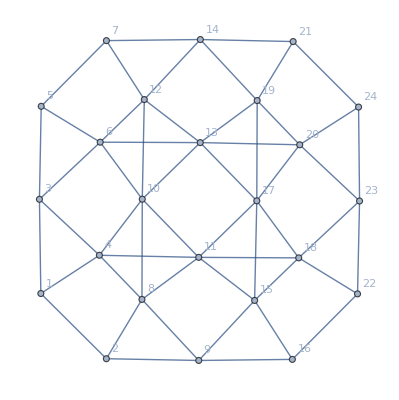

{-8.88178×10^-15,0.517887,0.712876,1.11816,1.53058}

{-8.88178×10^-15,0.56196,0.692296,1.21749,1.52691}

{-6.21725×10^-15,0.508198,0.725857,1.2186,1.54431}

{-1.15463×10^-14,0.477608,0.67321,1.00408,1.51865}

{-7.99361×10^-15,0.514434,0.702089,1.2245,1.55789}

{-8.88178×10^-15,0.589722,0.698716,1.32174,1.63426}

{-9.76996×10^-15,0.596029,0.643688,1.27384,1.59617}

{-9.76996×10^-15,0.526747,0.664978,1.13631,1.47946}

{-5.32907×10^-15,0.521229,0.665966,1.2792,1.43395}

{-9.76996×10^-15,0.641176,0.678989,1.51098,1.61254}

{-9.76996×10^-15,0.569208,0.62564,1.2045,1.5}

{-1.24345×10^-14,0.599435,0.648807,1.28624,1.69632}

{-9.76996×10^-15,0.582289,0.664792,1.26577,1.69915}

{-8.88178×10^-15,0.584244,0.6853,1.5328,1.83149}

{-8.88178×10^-15,0.431261,0.614304,0.905503,1.35119}

{-5.32907×10^-15,0.559121,0.60099,1.11214,1.64101}

{-7.10543×10^-15,0.582325,0.600308,1.24811,1.48273}

{-7.10543×10^-15,0.592956,0.636454,1.4154,1.68282}

{-6.21725×10^-15,0.501938,0.695994,1.24428,1.7912}

{-5.32907×10^-15,0.576395,0.695064,1.36797,1.67315}

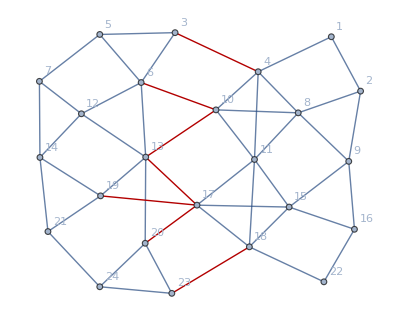
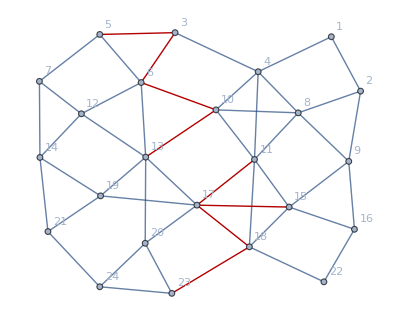
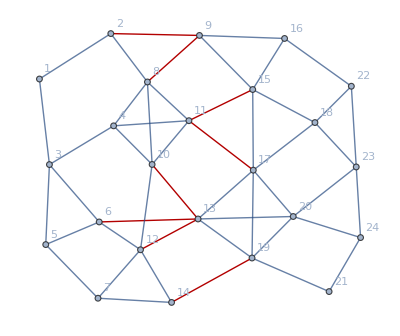
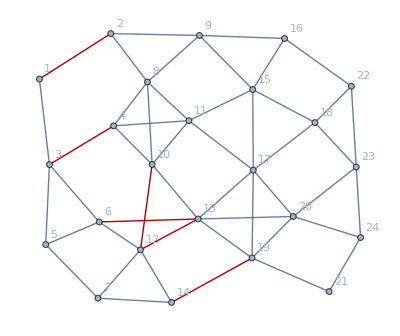
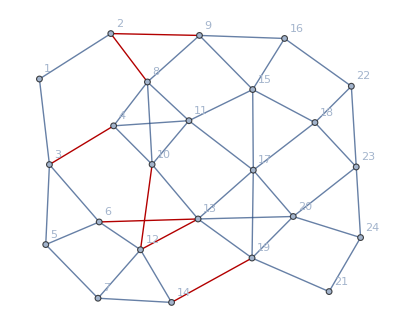
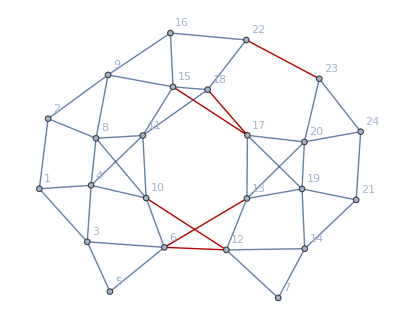
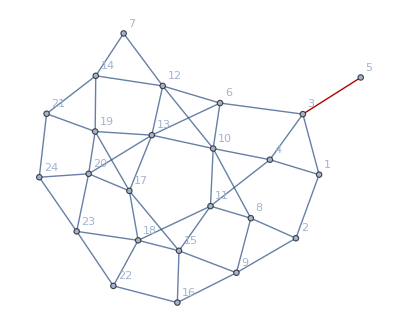
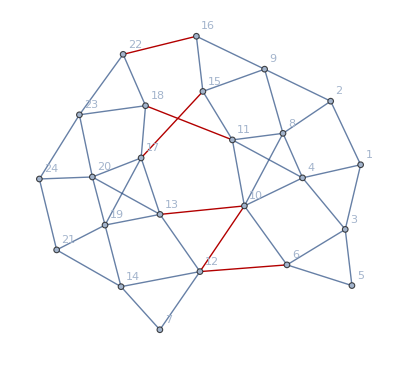
Spectral |  | Isoperimetric |  | MultipleFiedler |  | 
-Graphics- | 28. | -Graphics- | 32. | -Graphics- | 28. | 
-Graphics- | 32. | -Graphics- | 29.042 | -Graphics- | 31.5 | *
-Graphics- | 24.6857 | -Graphics- | 24.6857 | -Graphics- | 24.6857 | 
-Graphics- | 25.0435 | -Graphics- | 25.0435 | -Graphics- | 25.0435 | 
-Graphics- | 24. | -Graphics- | 36. | -Graphics- | 24. | 
-Graphics- | 32. | -Graphics- | 32. | -Graphics- | 28. | *
-Graphics- | 32.9143 | -Graphics- | 36. | -Graphics- | 28.8 | *
-Graphics- | 29.042 | -Graphics- | 27. | -Graphics- | 27. | *
-Graphics- | 28.8 | -Graphics- | 27. | -Graphics- | 28.8 | 
-Graphics- | 29.8667 | -Graphics- | 32. | -Graphics- | 29.8667 | 
-Graphics- | 29.042 | -Graphics- | 33.8824 | -Graphics- | 31.5 | 
-Graphics- | 32. | -Graphics- | 32.9143 | -Graphics- | 32. | 
-Graphics- | 29.8667 | -Graphics- | 32. | -Graphics- | 32. | 
-Graphics- | 28.1958 | -Graphics- | 29.8667 | -Graphics- | 28.1958 | 
-Graphics- | 25.0435 | -Graphics- | 25.0435 | -Graphics- | 25.0435 | 
-Graphics- | 26.1818 | -Graphics- | 30.3158 | -Graphics- | 26.1818 | 
-Graphics- | 33.8824 | -Graphics- | 32.2238 | -Graphics- | 32. | *
-Graphics- | 32. | -Graphics- | 31.5 | -Graphics- | 32. | 
-Graphics- | 28. | -Graphics- | 28.8 | -Graphics- | 27. | *
-Graphics- | 33.8824 | -Graphics- | 32.9143 | -Graphics- | 32. | *

```mathematica
g=LineGraph[GridGraph[{4,4}], VertexLabels->Automatic];
asyms=Table[EdgeDelete[g,EdgeList[g][[RandomSample[Range[Length[EdgeList[g]]],4]]]],20];
asyms =UndirectedGraph[#,VertexLabels->Automatic,VertexWeight->Table[1/V[#],V[#]], EdgeWeight->Automatic]&/@asyms;

examples=Map[With[{m1=EvaluatePartitionAlg[SpectralAlg, #], m2=EvaluatePartitionAlg[IsoperimetricAlg, #],
m3=EvaluatePartitionAlg[MultipleFiedlerAlg, #]},
{ShowCuttedEdges[#,m1[[3]]],N[m1[[2]]],
ShowCuttedEdges[#,m2[[3]]],N[m2[[2]]],
ShowCuttedEdges[#,m3[[3]]],N[m3[[2]]],
If [m1[[2]]>m3[[2]], "*",Nothing]}]&,asyms];
rowColors = Table[If[examples[[i, -1]]=="*",LightGreen,White] ,{i,1,Length[examples]}];
Grid[Prepend[examples,{"Spectral",Null,"Isoperimetric",Null,"MultipleFiedler",Null}], Alignment->Center, Frame->All, Background->{None, Prepend[rowColors,White]}]
```

```mathematica
Eigensystem[N[LaplacianMatrix[-Graphics-]]]
```

{{5.13204,4.71276,4.64846,4.34949,3.79076,3.71656,3.31112,3.,3.,2.16895,1.663,1.27594,0.738428,0.333412,0.159088,2.66423×10^-16},{{-0.559156,-0.0493141,0.0583504,0.124521,-0.302148,0.398721,-0.205214,0.326974,-0.0107512,-0.133183,-0.0301356,-0.085719,0.119392,-0.0301356,0.466449,-0.0886515},{0.174161,0.156316,-0.0468805,0.362892,-0.205215,-0.161272,-0.426062,-0.202997,-0.317209,-0.0819424,-0.0977418,0.528121,0.332391,-0.0977418,0.0659739,0.0172079},{0.0638868,0.281754,0.0547294,-0.395585,-0.410258,-0.273307,0.435254,-0.188261,-0.0818224,-0.240898,0.108425,-0.0486059,0.265309,0.108425,0.356254,-0.0353011},{0.0664698,0.582248,0.0951294,0.207895,0.0926678,0.248247,-0.156416,-0.433937,0.238875,-0.288675,-0.0620676,-0.24506,-0.316173,-0.0620676,0.0959897,-0.0631247},{0.155261,-0.171933,-0.158453,0.0728785,-0.21186,0.388327,-0.00540129,-0.341473,-0.0215987,0.190735,-0.0261142,-0.456934,0.495612,-0.0261142,-0.169628,0.286697},{0.175249,-0.379996,0.451945,0.234721,-0.423914,-0.205207,0.00461576,-0.124062,0.22411,0.102708,-0.0864039,-0.0328221,-0.351876,-0.0864039,0.203692,0.293644},{-0.124616,-0.114772,0.0908605,-0.532465,0.0723533,0.296917,-0.295126,-0.336258,-0.10364,0.0279614,0.230393,0.327367,-0.191482,0.230393,0.0781112,0.344004},{-1.11022×10^-16,0.,5.55112×10^-16,-4.44089×10^-16,2.24647×10^-16,3.88578×10^-16,-3.46945×10^-16,1.66533×10^-16,-1.11022×10^-16,-6.83581×10^-17,-0.707107,4.92508×10^-16,-3.33067×10^-16,0.707107,-1.66533×10^-16,0.},{0.206284,0.206284,0.412568,-0.206284,-0.412568,0.206284,-0.206284,0.206284,0.,0.206284,0.103142,-1.66533×10^-15,9.4369×10^-16,0.103142,-0.412568,-0.412568},{-0.496283,0.202926,0.31787,0.165518,0.00754694,0.0593134,0.420746,-0.221402,-0.376319,0.280684,-0.141596,0.124829,-0.0612507,-0.141596,-0.250347,0.10936},{-0.34283,0.168626,-0.297704,-0.0300114,-0.16766,-0.264513,-0.130658,-0.20006,0.555389,0.518791,0.0452662,0.119834,0.0673334,0.0452662,0.00620795,-0.093277},{0.245162,-0.134272,-0.112506,0.00863992,0.10343,0.164344,0.0775171,-0.217386,-0.309686,0.471569,-0.0313107,-0.0393402,-0.184891,-0.0313107,0.475715,-0.485676},{0.153953,-0.066684,-0.329969,-0.0680746,-0.262487,0.434622,0.366548,0.0234266,0.244643,-0.139949,-0.260252,0.462427,-0.153793,-0.260252,-0.109872,-0.0342885},{-0.101377,-0.328505,0.425577,-0.0899845,0.311184,0.0269268,0.0300339,-0.3034,0.32475,-0.193426,-0.134993,0.143146,0.398078,-0.134993,0.00614291,-0.379161},{0.123285,0.250094,0.140358,-0.403752,0.150197,-0.0495358,-0.186752,0.221627,0.0168017,0.232626,-0.480136,-0.0772591,0.10819,-0.480136,0.17815,0.256243},{0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25,0.25}}}